```mathematica
MaxDifference[tuple_] :=MaxDifference[tuple]=Module[
{current,diff,max=0, i, last,list=GoodForTuple[tuple]},
Monitor[
last=list[[1]];
For[i=2,i<Length[list], i++,
current=list[[i]];
diff = current-last;
If [diff >max, max= diff];
last = current;
],
{tuple,i}];
max
]
```

```mathematica
MaxDifference2[tuple_]:=MaxDifference2[tuple]=Max[Differences[GoodForTuple[tuple]]]
```

```mathematica
MeanDifference2[tuple_]:=MeanDifference2[tuple]=N[Mean[Differences[GoodForTuple[tuple]]]]
```

```mathematica
Clear[MyAccLast]
```

```mathematica
MaxDifference[{5,7,13}]
```

1668677658126502878408200723

```mathematica
MaxDifference2[{5,7,13}]
```

1668677658126502878408200723

```mathematica
res2=Monitor[
Table[
{tuple, MeanDifference2[tuple]},
{tuple,Select[
Prime[Subsets[Range[2,10],{4}]],
magicGraham[#]>0&]}
],tuple]
```

{{{3,17,23,29},Mean[{}]},{{3,19,23,29},1.2495×10^37},{{5,11,17,29},7.27685×10^34},{{5,11,19,23},2.34636×10^27},{{5,11,19,29},2.67192×10^33},{{5,11,23,29},7.11272×10^36},{{5,13,17,23},2.03735×10^37},{{5,13,17,29},7.08915×10^36},{{5,13,19,23},6.61393×10^34},{{5,13,19,29},1.73411×10^29},{{5,13,23,29},5.62942×10^89},{{5,17,19,23},2.40048×10^103},{{5,17,19,29},3.89186×10^72},{{5,17,23,29},1.80645×10^65},{{5,19,23,29},6.74665×10^55},{{7,11,13,19},1.9220105023644×10^2196},{{7,11,13,23},1.43257×10^35},{{7,11,13,29},3.23985×10^33},{{7,11,17,19},1.4292×10^186},{{7,11,17,23},1.35391×10^122},{{7,11,17,29},2.72818×10^80},{{7,11,19,23},3.13575×10^90},{{7,11,19,29},1.1929×10^71},{{7,11,23,29},4.87435×10^58},{{7,13,17,19},1.19021×10^118},{{7,13,17,23},1.03506×10^83},{{7,13,17,29},1.8585×10^65},{{7,13,19,23},1.62244×10^78},{{7,13,19,29},3.07561×10^55},{{7,13,23,29},4.26158×10^49},{{7,17,19,23},7.2146×10^50},{{7,17,19,29},5.95871×10^45},{{7,17,23,29},6.48866×10^41},{{7,19,23,29},5.50592×10^37},{{11,13,17,19},3.92781×10^79},{{11,13,17,23},3.1992×10^45},{{11,13,17,29},8.37799×10^39},{{11,13,19,23},1.28423×10^44},{{11,13,19,29},5.16369×10^37},{{11,13,23,29},2.54378×10^34},{{11,17,19,23},2.17564×10^41},{{11,17,19,29},9.80625×10^35},{{11,17,23,29},8.93584×10^32},{{11,19,23,29},4.8229×10^33},{{13,17,19,23},2.75667×10^33},{{13,17,19,29},1.32471×10^33},{{13,17,23,29},1.71077×10^31},{{13,19,23,29},1.12006×10^25},{{17,19,23,29},7.55783×10^23}}

```mathematica
Clear[MeanDifference2]
```

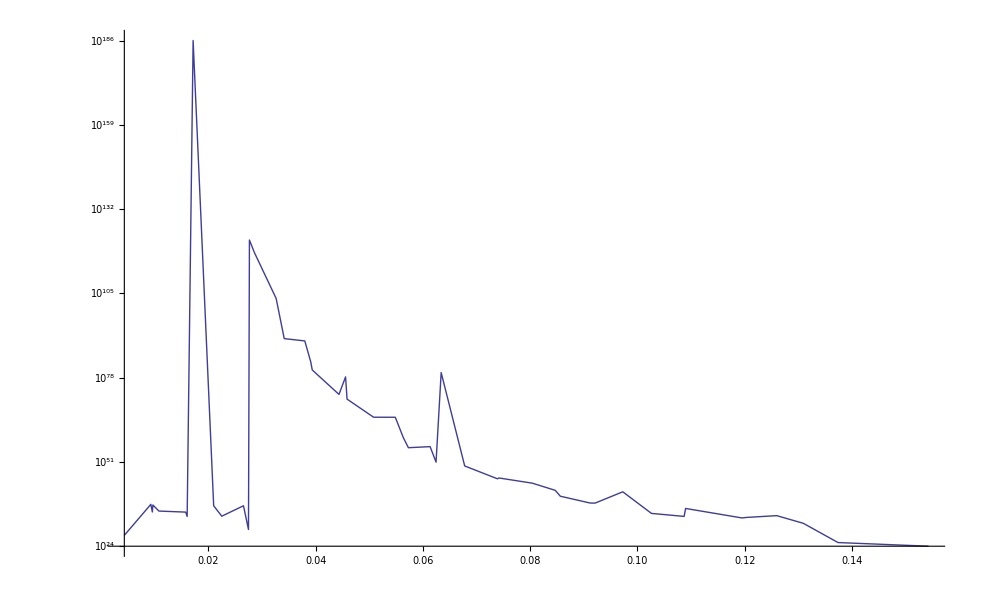

```mathematica
ListLogPlot[Map[{magicGraham[#[[1]]],#[[2]]}&,Sort[res2,magicGraham[#1[[1]]]>magicGraham[#2[[1]]]&]],Joined->True,PlotRange->All]
```

```mathematica
res3=Select[Monitor[
Table[
{tuple, MeanDifferenceLimit[tuple]},
{tuple,Select[
Subsets[Prime[Range[2,25]],{4}],
magicGraham[#]>0&]}
],tuple]
,#[[2]]≠0&
]
```

{{{3,5,67,89},2.1544499297697×10^459},{{3,5,67,97},1.29959×10^227},{{3,5,71,83},4.36707467764187×10^529},{{3,5,71,89},2.74896×10^186},{{3,5,71,97},2.07274×10^147},{{3,5,73,83},3.31023802578005×10^310},{{3,5,73,89},1.81591×10^162},{{3,5,73,97},6.68966×10^115},{{3,5,79,83},1.08124×10^218},{{3,5,79,89},1.35611×10^162},{{3,5,79,97},8.44679×10^102},{{3,5,83,89},3.59171×10^110},«10112»,{{71,73,83,97},1953.54},{{71,73,89,97},3655.35},{{71,79,83,89},732.064},{{71,79,83,97},152.385},{{71,79,89,97},2175.86},{{71,83,89,97},2912.16},{{73,79,83,89},3132.75},{{73,79,83,97},1181.39},{{73,79,89,97},2119.35},{{73,83,89,97},2903.42},{{79,83,89,97},208.302}}

```mathematica
MaxList[height_]:=Select[Monitor[
Table[
{tuple, MyMaxValue[tuple,height]},
{tuple,Subsets[Prime[Range[2,20]],{4,5}]}
],{tuple,height}]
,#[[2]]≠0&
]
```

```mathematica
Clear[MeanDifferenceLimit]
```

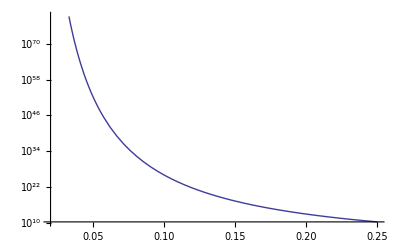

```mathematica
LogPlot[Exp[(6/x)],{x,0.02,0.25}]
```

```mathematica
FullSimplify[Exp[(1/x)]]
```

ⅇ^(1/x)

```mathematica
First[Sort[Map[{N[magicGraham[#[[1]]]],#[[1]],#[[2]]}&,res3]]]
```

{0.000302007,{7,11,13,19},2.90089402687325×10^2196}

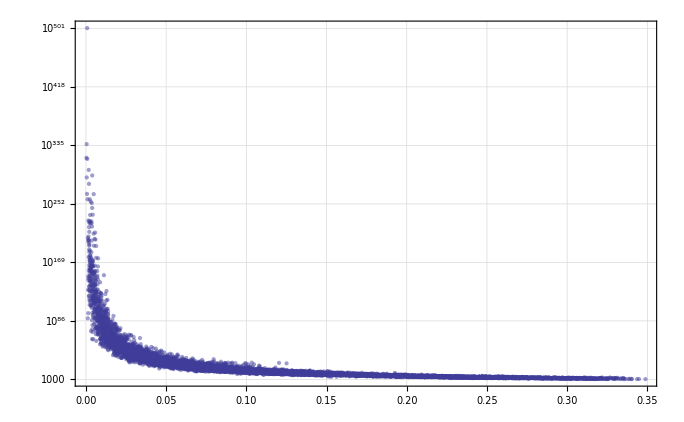

```mathematica
ListLogPlot[Table[
Sort[
Select[Map[{N[magicGraham[#[[1]]]],#[[2]]}&,MaxList[height]],Abs[#[[1]]]<5&]
]
,{height,1000,1000,100}],Joined->False, PlotRange->All, PlotStyle->Opacity[0.5],GridLines->Automatic, AxesOrigin->{0,0}, Frame->True]
```

```mathematica
data=Sort[Map[{N[magicGraham[#[[1]]]]+1,N[Log[#[[2]]]]}&,MaxList[80]]]
```

{{0.957053,73.8077},{0.959737,55.2126},{0.960014,55.5162},{0.960761,73.4929},{0.961044,66.3189},{0.961088,73.7564},{0.961973,17.3232},{0.962912,103.646},{0.96407,51.9632},{0.964268,35.6554},{0.964495,71.1913},{0.964858,57.5308},«7938»,{1.33491,4.43082},{1.3353,5.27007},{1.33558,4.17517},{1.33651,5.25618},{1.33827,5.24282},{1.33891,2.62173},{1.34012,4.18466},{1.34027,2.75261},{1.3436,2.56689},{1.34481,2.73716},{1.34882,2.54429}}

```mathematica
FindFit[data,a (x+b)^( c ),{a,b,c,d},x]
```

FindFit::nrlnum: The function value {-64.52361116004694` - 24.57948968590835` ⅈ, -45.926544971074904` - 24.58460430589054` ⅈ, -46.23002109470667` - 24.585132062585917` ⅈ, -64.20618439498209` - 24.586554668028427` ⅈ, -57.03195931549431` - 24.587095751278373` ⅈ, -« 18 » - « 1 », -8.035535620813427` - « 18 » ⅈ, -94.35756099102217` - 24.590658946934973` ⅈ, -42.67405951262196` - 24.592867191069175` ⅈ, -26.366167154667806` - 24.593244988423734` ⅈ, « 7951 »} is not a list of real numbers with dimensions {7961} at {a, b, c, d} = {48.70931493206316`, -5.925630226401086`, -0.385042278862458`, 1.`}.

{a→48.7093,b→-5.92563,c→-0.385042,d→1.}

```mathematica
a (x+b)^( c )/.{a->48.70931493206316,b->-5.925630226401086,c->-0.385042278862458,d->1.}
```

48.7093/(-5.92563+x)^0.385042

```mathematica
Table[41* (169)^x,{x,1,20}]
```

{6929,1171001,197899169,33444959561,5652198165809,955221490021721,161432431813670849,27282080976510373481,4610671685030253118289,779203514770112776990841,131685393996149059311452129,22254831585349191023635409801,3761066537924013282994384256369,635620244909158244826050939326361,107419821389647743375602608746155009,18153949814850468630476840878100196521,3068017518709729198550586108398933212049,518494960661944234555049052319419712836281,87625648351868575639803289841981931469331489,14808734571465789283126755983294946418317021641}

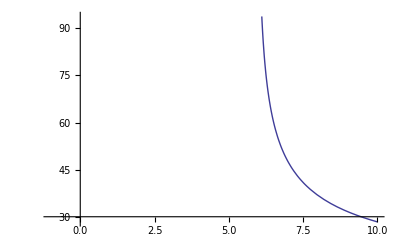

```mathematica
Plot[48.70931493206316/(-5.925630226401086+x)^0.385042278862458,{x,-1,10}]
```

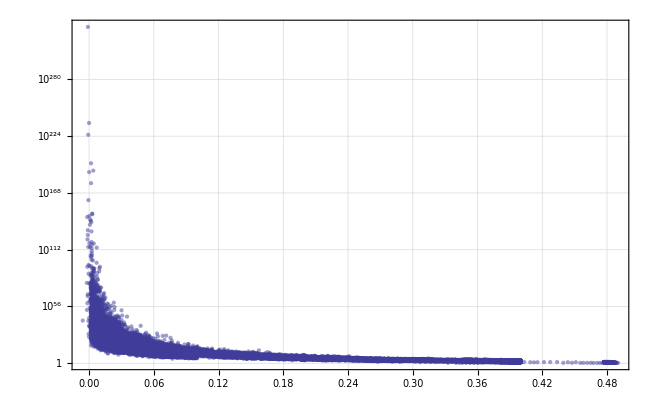

```mathematica
ListLogPlot[Table[
Sort[
Select[Map[{N[magicGraham[#[[1]]]],#[[2]]}&,MaxList[height]],Abs[#[[1]]]<1&]
]
,{height,200,200,100}],Joined->False, PlotRange->All, PlotStyle->Opacity[0.5],GridLines->Automatic, AxesOrigin->{0,0}, Frame->True]
```

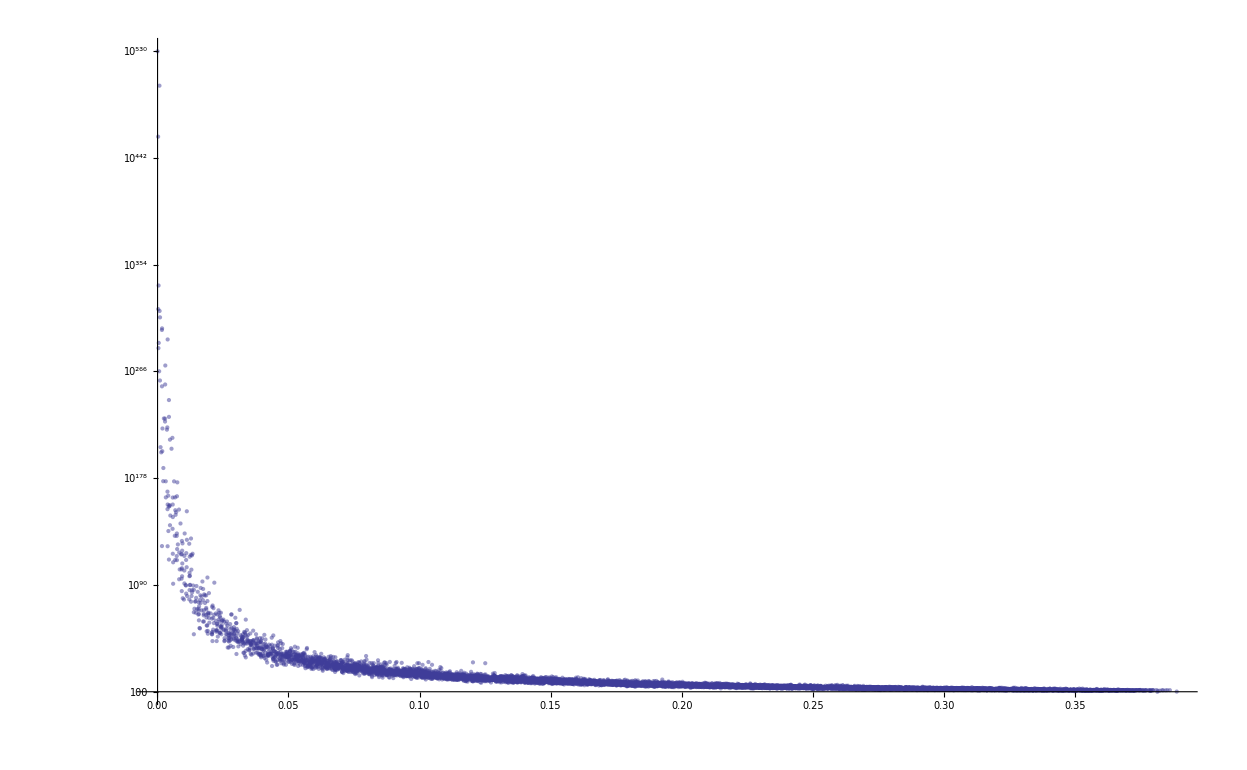

```mathematica
ListLogPlot[Map[{N[magicGraham[#[[1]]]],#[[2]]}&,res3],Joined->False, PlotRange->All, PlotStyle->Opacity[0.5]]
```

```mathematica
CalcGoodForTuple[{7,11,13,19},50000]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 7546

$Aborted

```mathematica
points=Map[{N[magicGraham[#[[1]]]],Log[#[[2]]]}&,Sort[res3,magicGraham[#1[[1]]]>magicGraham[#2[[1]]]&]]
```

{{0.388884,8.17635},{0.386256,10.6237},{0.385313,10.5447},{0.384651,9.8028},{0.383708,10.1639},{0.383313,10.6063},{0.382433,9.87186},{0.381708,10.1374},{0.38149,7.64919},{0.38108,8.74106},{0.379982,10.5694},«9846»,{0.0304478,176.429},{0.0304391,147.596},{0.0302839,146.047},{0.0301595,136.606},{0.0300995,146.388},{0.030098,155.648},{0.0286041,149.392},{0.0276687,147.443},{0.0171715,254.241},{0.000302007,5057.541883189535362}}

```mathematica
ExpectedValue[AppendTo[points,{0,Infinity}]]
```

```mathematica
NonlinearModelFit[points, a/(b x), {a,b},x]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[1.6957/x]

```mathematica
Plot[-12/Log[-16x],{x,0.02,0.25}]
```

-Graphics-

```mathematica
FindFit[points, a /(x ), {a,b,c,d},x]
```

{a→6.76848,b→0.,c→0.,d→0.}

```mathematica
Exp[Exp[6.768477114116696]]
```

6.762652543512×10^377

```mathematica
N[Log[50000]]/2
```

5.40989

```mathematica
MyMaxValue[tuple_,limit_]:=
Module[
{good, result=0,fileName= FileNameForTuple[tuple]},
If[FileExistsQ[fileName],
good= ReadList[fileName,Expression, limit];
If[Length[good] == limit,
result=N[Mean[Differences[good]]];
MyMaxValue[tuple,limit]=result
]
];
result
]
```

```mathematica
Clear[MaxValue]
```

Clear::wrsym: Symbol MaxValue is Protected.

```mathematica
MeanDifferenceLimit[tuple_]:=
Module[
{good, limit=1000, result=0,fileName= FileNameForTuple[tuple]},
If[FileExistsQ[fileName],
good= ReadList[fileName,Expression, limit];
If[Length[good] == limit,
result=N[Mean[Differences[good]]];
MeanDifferenceLimit[tuple]=result
]
];
result
]
```

```mathematica
Clear[MeanDifferenceLimit]
```

```mathematica
ListLogPlot[Map[{magicGraham[#[[1]]],#[[2]]}&,Sort[res2,magicGraham[#1[[1]]]>magicGraham[#2[[1]]]&]],Joined->True,PlotRange->All]
```

```mathematica
MeanDifferenceLimit[{3,5,7}]
```

2.43999×10^62

```mathematica
With[
{all=Sort[Select[
Prime[Subsets[Range[2,10],{4}]],
magicGraham[#]>0&],magicGraham[#1]>magicGraham[#2]&]},
Monitor[
Table[
CalcGoodForTuple[all[[pos]],500000],
{pos, 1, Length[all]}
],{pos,Length[all]}
]
]
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

General::stop: Further output of ParallelTable will be suppressed during this calculation.

Aborted at value : 156541

$Aborted

```mathematica
CloseStreams[]
```

Closing d:\triangle\DataSrc\17\41\47\53\Solutions.txt

Closing d:\triangle\DataSrc\13\17\19\29\Solutions.txt

```mathematica
MaxDifference2[{3,31,43,173,229}]
```

```mathematica
N[Log[354465153353424792190602644266211738085104389893488821153485750923471806005402536343858457905408680150888838263228091258021145605962524133883097364115152674955356895609311978059216288134651192101537729184715491169867017640970551208375891870451321528577066857250262689318298055162138965030145811974807816832259591680446914827095209361278911125107762269605486573579809852595383770839112965397408972655911053770823960547507290042418372723424489514020466355105211288348874885050290468867040651062096372077355206200438124116132381704648769499657929197904068399439553501581493150294494958186707487989576771587345012238586972777003023136808528489928323695379515392703868544216813657553966299118661049422820210943517818567461629593553686790353332815899108271796332708407029303638178777033021576150130081727925907562066764464258450113699456025505553812037456449344516781981124643684325080376610819708564989507909230795213980182886395641092212031660521846711176953929390885455899806817120557248141149374566510726844054782561346648157551465411832282144511850337939064933654631303232844781594116784950133848687793220253484505710622477920057411680735809667118820039012144132030447583355665466050177641524867395722780299432410917444312974771501490394326840705736638266982364336130067909094289993606388762817712272686901982693677142527916798473215329248549585428484372928068987639237110446465046601874687]]
```

3197.25

```mathematica
Export["c:\\temp\\exp.xls",Map[{N[magicGraham[#[[1]]]],N[Log[#[[2]]]]}&,MaxList[80]],"XLS"]
```

c:\temp\exp.xls